```mathematica
f:=Compile[{{n,_Integer},{z,_Complex}},
Module[{n1=n,w=z,k=0,u=I},
u=0;While[k<n1,u=u^2+w;Print[N[u]]
;k=k+1
;]]
]
F[n_,z_]:=
Module[{w=z,u=0,k=0},
While[k<n,u=u^2+w;Print[N[u]]
;k=k+1
;]]

Timing[f[25,0.25]]
Timing[F[25,0.25]]
```

0.25

0.3125

0.347656

0.370865

0.387541

0.400188

0.41015

0.418223

0.424911

0.430549

0.435373

0.439549

0.443204

0.446429

0.449299

0.45187

0.454186

0.456285

0.458196

0.459944

0.461548

0.463027

0.464394

0.465662

0.466841

{0.,Null}

0.25

0.3125

0.347656

0.370865

0.387541

0.400188

0.41015

0.418223

0.424911

0.430549

0.435373

0.439549

0.443204

0.446429

0.449299

0.45187

0.454186

0.456285

0.458196

0.459944

0.461548

0.463027

0.464394

0.465662

0.466841

{0.,Null}

```mathematica
Grille[n_,z1_,z2_]:=
Module[{xmax=Re[z1],ymax=Im[z1],xmin=Re[z2],ymin=Im[z2],n1=1-1,Absc,Ordo,Points},
Absc=Table[k((xmax-xmin)/n)+xmin,{k,0,n1}];
Ordo=Table[k((ymax-ymin)/n)+ymin,{k,0,n1}];
Points=Outer[#1+I*#2&,Absc,Ordo]
]
```

{{0,(5 ⅈ)/12,(5 ⅈ)/6,(5 ⅈ)/4,(5 ⅈ)/3,(25 ⅈ)/12,(5 ⅈ)/2,(35 ⅈ)/12,(10 ⅈ)/3,(15 ⅈ)/4,(25 ⅈ)/6,(55 ⅈ)/12},{5/12,5/12+(5 ⅈ)/12,5/12+(5 ⅈ)/6,5/12+(5 ⅈ)/4,5/12+(5 ⅈ)/3,5/12+(25 ⅈ)/12,5/12+(5 ⅈ)/2,5/12+(35 ⅈ)/12,5/12+(10 ⅈ)/3,5/12+(15 ⅈ)/4,5/12+(25 ⅈ)/6,5/12+(55 ⅈ)/12},{5/6,5/6+(5 ⅈ)/12,5/6+(5 ⅈ)/6,5/6+(5 ⅈ)/4,5/6+(5 ⅈ)/3,5/6+(25 ⅈ)/12,5/6+(5 ⅈ)/2,5/6+(35 ⅈ)/12,5/6+(10 ⅈ)/3,5/6+(15 ⅈ)/4,5/6+(25 ⅈ)/6,5/6+(55 ⅈ)/12},{5/4,5/4+(5 ⅈ)/12,5/4+(5 ⅈ)/6,5/4+(5 ⅈ)/4,5/4+(5 ⅈ)/3,5/4+(25 ⅈ)/12,5/4+(5 ⅈ)/2,5/4+(35 ⅈ)/12,5/4+(10 ⅈ)/3,5/4+(15 ⅈ)/4,5/4+(25 ⅈ)/6,5/4+(55 ⅈ)/12},{5/3,5/3+(5 ⅈ)/12,5/3+(5 ⅈ)/6,5/3+(5 ⅈ)/4,5/3+(5 ⅈ)/3,5/3+(25 ⅈ)/12,5/3+(5 ⅈ)/2,5/3+(35 ⅈ)/12,5/3+(10 ⅈ)/3,5/3+(15 ⅈ)/4,5/3+(25 ⅈ)/6,5/3+(55 ⅈ)/12},{25/12,25/12+(5 ⅈ)/12,25/12+(5 ⅈ)/6,25/12+(5 ⅈ)/4,25/12+(5 ⅈ)/3,25/12+(25 ⅈ)/12,25/12+(5 ⅈ)/2,25/12+(35 ⅈ)/12,25/12+(10 ⅈ)/3,25/12+(15 ⅈ)/4,25/12+(25 ⅈ)/6,25/12+(55 ⅈ)/12},{5/2,5/2+(5 ⅈ)/12,5/2+(5 ⅈ)/6,5/2+(5 ⅈ)/4,5/2+(5 ⅈ)/3,5/2+(25 ⅈ)/12,5/2+(5 ⅈ)/2,5/2+(35 ⅈ)/12,5/2+(10 ⅈ)/3,5/2+(15 ⅈ)/4,5/2+(25 ⅈ)/6,5/2+(55 ⅈ)/12},{35/12,35/12+(5 ⅈ)/12,35/12+(5 ⅈ)/6,35/12+(5 ⅈ)/4,35/12+(5 ⅈ)/3,35/12+(25 ⅈ)/12,35/12+(5 ⅈ)/2,35/12+(35 ⅈ)/12,35/12+(10 ⅈ)/3,35/12+(15 ⅈ)/4,35/12+(25 ⅈ)/6,35/12+(55 ⅈ)/12},{10/3,10/3+(5 ⅈ)/12,10/3+(5 ⅈ)/6,10/3+(5 ⅈ)/4,10/3+(5 ⅈ)/3,10/3+(25 ⅈ)/12,10/3+(5 ⅈ)/2,10/3+(35 ⅈ)/12,10/3+(10 ⅈ)/3,10/3+(15 ⅈ)/4,10/3+(25 ⅈ)/6,10/3+(55 ⅈ)/12},{15/4,15/4+(5 ⅈ)/12,15/4+(5 ⅈ)/6,15/4+(5 ⅈ)/4,15/4+(5 ⅈ)/3,15/4+(25 ⅈ)/12,15/4+(5 ⅈ)/2,15/4+(35 ⅈ)/12,15/4+(10 ⅈ)/3,15/4+(15 ⅈ)/4,15/4+(25 ⅈ)/6,15/4+(55 ⅈ)/12},{25/6,25/6+(5 ⅈ)/12,25/6+(5 ⅈ)/6,25/6+(5 ⅈ)/4,25/6+(5 ⅈ)/3,25/6+(25 ⅈ)/12,25/6+(5 ⅈ)/2,25/6+(35 ⅈ)/12,25/6+(10 ⅈ)/3,25/6+(15 ⅈ)/4,25/6+(25 ⅈ)/6,25/6+(55 ⅈ)/12},{55/12,55/12+(5 ⅈ)/12,55/12+(5 ⅈ)/6,55/12+(5 ⅈ)/4,55/12+(5 ⅈ)/3,55/12+(25 ⅈ)/12,55/12+(5 ⅈ)/2,55/12+(35 ⅈ)/12,55/12+(10 ⅈ)/3,55/12+(15 ⅈ)/4,55/12+(25 ⅈ)/6,55/12+(55 ⅈ)/12}}

Set::write: Tag Times in {0, 1, 2, 3, 4, 5}\ {{0, ⅈ, 2\ ⅈ, 3\ ⅈ, 4\ ⅈ, 5\ ⅈ, 6\ ⅈ, 7\ ⅈ, 8\ ⅈ, 9\ ⅈ, 10\ ⅈ, 11\ ⅈ}, {1, 1 + ⅈ, 1 + 2\ ⅈ, 1 + 3\ ⅈ, 1 + 4\ ⅈ, 1 + 5\ ⅈ, 1 + 6\ ⅈ, 1 + 7\ ⅈ, 1 + 8\ ⅈ, 1 + 9\ ⅈ, 1 + 10\ ⅈ, 1 + 11\ ⅈ}, {2, 2 + ⅈ, 2 + 2\ ⅈ, 2 + 3\ ⅈ, 2 + 4\ ⅈ, 2 + 5\ ⅈ, 2 + 6\ ⅈ, 2 + 7\ ⅈ, 2 + 8\ ⅈ, 2 + 9\ ⅈ, 2 + 10\ ⅈ, 2 + 11\ ⅈ}, « 6 », {9, 9 + ⅈ, 9 + 2\ ⅈ, 9 + 3\ ⅈ, 9 + 4\ ⅈ, 9 + 5\ ⅈ, 9 + 6\ ⅈ, 9 + 7\ ⅈ, 9 + 8\ ⅈ, 9 + 9\ ⅈ, 9 + 10\ ⅈ, 9 + 11\ ⅈ}, {10, 10 + ⅈ, 10 + 2\ ⅈ, 10 + 3\ ⅈ, 10 + 4\ ⅈ, 10 + 5\ ⅈ, 10 + 6\ ⅈ, 10 + 7\ ⅈ, 10 + 8\ ⅈ, 10 + 9\ ⅈ, 10 + 10\ ⅈ, 10 + 11\ ⅈ}, {11, 11 + ⅈ, 11 + 2\ ⅈ, 11 + 3\ ⅈ, 11 + 4\ ⅈ, 11 + 5\ ⅈ, 11 + 6\ ⅈ, 11 + 7\ ⅈ, 11 + 8\ ⅈ, 11 + 9\ ⅈ, 11 + 10\ ⅈ, 11 + 11\ ⅈ}} is Protected.

Set::write: Tag Times in {0, 1, 2, 3, 4, 5}\ {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11} is Protected.

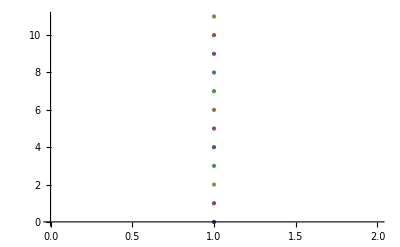
{{{0,ⅈ -Graphics-,2 ⅈ -Graphics-,3 ⅈ -Graphics-,4 ⅈ -Graphics-,5 ⅈ -Graphics-,6 ⅈ -Graphics-,7 ⅈ -Graphics-,8 ⅈ -Graphics-,9 ⅈ -Graphics-,10 ⅈ -Graphics-,11 ⅈ -Graphics-},{ⅈ -Graphics-^2,(ⅈ+ⅈ -Graphics-) -Graphics-,(2 ⅈ+ⅈ -Graphics-) -Graphics-,(3 ⅈ+ⅈ -Graphics-) -Graphics-,(4 ⅈ+ⅈ -Graphics-) -Graphics-,(5 ⅈ+ⅈ -Graphics-) -Graphics-,(6 ⅈ+ⅈ -Graphics-) -Graphics-,(7 ⅈ+ⅈ -Graphics-) -Graphics-,(8 ⅈ+ⅈ -Graphics-) -Graphics-,(9 ⅈ+ⅈ -Graphics-) -Graphics-,(10 ⅈ+ⅈ -Graphics-) -Graphics-,(11 ⅈ+ⅈ -Graphics-) -Graphics-},«8»,{10 ⅈ -Graphics-^2,(ⅈ+10 ⅈ -Graphics-) -Graphics-,(2 ⅈ+10 ⅈ -Graphics-) -Graphics-,(3 ⅈ+10 ⅈ -Graphics-) -Graphics-,(4 ⅈ+10 ⅈ -Graphics-) -Graphics-,(5 ⅈ+10 ⅈ -Graphics-) -Graphics-,(6 ⅈ+10 ⅈ -Graphics-) -Graphics-,(7 ⅈ+10 ⅈ -Graphics-) -Graphics-,(8 ⅈ+10 ⅈ -Graphics-) -Graphics-,(9 ⅈ+10 ⅈ -Graphics-) -Graphics-,(10 ⅈ+10 ⅈ -Graphics-) -Graphics-,(11 ⅈ+10 ⅈ -Graphics-) -Graphics-},{11 ⅈ -Graphics-^2,(ⅈ+11 ⅈ -Graphics-) -Graphics-,(2 ⅈ+11 ⅈ -Graphics-) -Graphics-,(3 ⅈ+11 ⅈ -Graphics-) -Graphics-,(4 ⅈ+11 ⅈ -Graphics-) -Graphics-,(5 ⅈ+11 ⅈ -Graphics-) -Graphics-,(6 ⅈ+11 ⅈ -Graphics-) -Graphics-,(7 ⅈ+11 ⅈ -Graphics-) -Graphics-,(8 ⅈ+11 ⅈ -Graphics-) -Graphics-,(9 ⅈ+11 ⅈ -Graphics-) -Graphics-,(10 ⅈ+11 ⅈ -Graphics-) -Graphics-,(11 ⅈ+11 ⅈ -Graphics-) -Graphics-}},«10»,{{«1»},«10»,{«1»}}}

```mathematica
Grille[0,5,0,5,12]
```

```mathematica
Hauteur[z1_]:=
Module[{z=z1,N=2,l=0},
While[l<20,If[
```